```mathematica
xval = {0, 0.001, 0.01, 0.1, 2}         
F[s_]:= Log[s+1]
yval = F[xval]
yvalprime = F'[xval]
yvaldoubprime = F''[xval]      

numparts = Length[xval]       (*Set the number of data points to the length of its vector*)
n = numparts-1                 

Do[{xx[k-1]=xval[[k]],               
yy[k-1]=yval[[k]],
yyprime[k-1]=yvalprime[[k]],
yydoubprime[k-1]=yvaldoubprime[[k]]},
{k,1,numparts}]

Table[{xx[k],yy[k]},{k, 0, n}];
Unknowns=Table[{a[k],b[k],c[k],d[k]},{k,0,n-1}] // Flatten           

Do[P[k][x_]= a[k]*(x)^3+b[k]*(x)^2+c[k]*(x)+d[k], {k,0,n-1}]             (*Everything above this comment is ok, refer to comments for those from 3-point cubic spline case.*)
P[0][x]

Do[EquationA[k] = P[k][xx[k]] == yy[k] , {k,0,n-1}]
TableA=Table[EquationA[k],{k,0,n-1}]

Do[EquationB[k] =  P[k][xx[k+1]] == yy[k+1] , {k, 0, n-1}]  
TableB=Table[EquationB[k],{k,0,n-1}]                               (*These four conditions should be put into a "Do" or a "For" loop*)

EquationC = { P[0]'[xx[0]]== yyprime[0]}
EquationD = {P[n-1]'[xx[n]]== yyprime[n]}

Do[EquationE[k] =  P[k-1]'[xx[k]] == P[k]'[xx[k]] , {k,1,n-1}]
TableE=Table[EquationE[k],{k,1,n-1}]

Do[EquationF[k] =  P[k-1]''[xx[k]] == P[k]''[xx[k]] , {k,1,n-1}]
TableF=Table[EquationF[k],{k,1,n-1}]

AllEquationsToSolve=Join[TableA,TableB,EquationC,EquationD,TableE,TableF]

Solve[AllEquationsToSolve, Unknowns]
```

{0,0.001,0.01,0.1,2}

{0,0.0009995,0.00995033,0.0953102,Log[3]}

{1,0.999001,0.990099,0.909091,1/3}

{-1,-0.998003,-0.980296,-0.826446,-1/9}

5

4

{a[0],b[0],c[0],d[0],a[1],b[1],c[1],d[1],a[2],b[2],c[2],d[2],a[3],b[3],c[3],d[3]}

x^3 a[0]+x^2 b[0]+x c[0]+d[0]

{d[0]==0,1.×10^-9 a[1]+1.×10^-6 b[1]+0.001 c[1]+d[1]==0.0009995,1.×10^-6 a[2]+0.0001 b[2]+0.01 c[2]+d[2]==0.00995033,0.001 a[3]+0.01 b[3]+0.1 c[3]+d[3]==0.0953102}

{1.×10^-9 a[0]+1.×10^-6 b[0]+0.001 c[0]+d[0]==0.0009995,1.×10^-6 a[1]+0.0001 b[1]+0.01 c[1]+d[1]==0.00995033,0.001 a[2]+0.01 b[2]+0.1 c[2]+d[2]==0.0953102,8 a[3]+4 b[3]+2 c[3]+d[3]==Log[3]}

{c[0]==1}

{12 a[3]+4 b[3]+c[3]==1/3}

{3.×10^-6 a[0]+0.002 b[0]+c[0]==3.×10^-6 a[1]+0.002 b[1]+c[1],0.0003 a[1]+0.02 b[1]+c[1]==0.0003 a[2]+0.02 b[2]+c[2],0.03 a[2]+0.2 b[2]+c[2]==0.03 a[3]+0.2 b[3]+c[3]}

{0.006 a[0]+2 b[0]==0.006 a[1]+2 b[1],0.06 a[1]+2 b[1]==0.06 a[2]+2 b[2],0.6 a[2]+2 b[2]==0.6 a[3]+2 b[3]}

{d[0]==0,1.×10^-9 a[1]+1.×10^-6 b[1]+0.001 c[1]+d[1]==0.0009995,1.×10^-6 a[2]+0.0001 b[2]+0.01 c[2]+d[2]==0.00995033,0.001 a[3]+0.01 b[3]+0.1 c[3]+d[3]==0.0953102,1.×10^-9 a[0]+1.×10^-6 b[0]+0.001 c[0]+d[0]==0.0009995,1.×10^-6 a[1]+0.0001 b[1]+0.01 c[1]+d[1]==0.00995033,0.001 a[2]+0.01 b[2]+0.1 c[2]+d[2]==0.0953102,8 a[3]+4 b[3]+2 c[3]+d[3]==Log[3],c[0]==1,12 a[3]+4 b[3]+c[3]==1/3,3.×10^-6 a[0]+0.002 b[0]+c[0]==3.×10^-6 a[1]+0.002 b[1]+c[1],0.0003 a[1]+0.02 b[1]+c[1]==0.0003 a[2]+0.02 b[2]+c[2],0.03 a[2]+0.2 b[2]+c[2]==0.03 a[3]+0.2 b[3]+c[3],0.006 a[0]+2 b[0]==0.006 a[1]+2 b[1],0.06 a[1]+2 b[1]==0.06 a[2]+2 b[2],0.6 a[2]+2 b[2]==0.6 a[3]+2 b[3]}

{{a[0]→11.5333,b[0]→-0.5112,c[0]→1.,d[0]→0.,a[1]→-2.29718,b[1]→-0.469709,c[1]→0.999959,d[1]→1.38305×10^-8,a[2]→0.869602,b[2]→-0.564712,c[2]→1.00091,d[2]→-3.15296×10^-6,a[3]→0.0529861,b[3]→-0.319728,c[3]→0.97641,d[3]→0.000813463}}

```mathematica
{c[0]==0}-
```

{12 a[3]+4 b[3]+c[3]==32}

{3.×10^-6 a[0]+0.002 b[0]+c[0]==3.×10^-6 a[1]+0.002 b[1]+c[1],0.0003 a[1]+0.02 b[1]+c[1]==0.0003 a[2]+0.02 b[2]+c[2],0.03 a[2]+0.2 b[2]+c[2]==0.03 a[3]+0.2 b[3]+c[3]}

{0.006 a[0]+2 b[0]==0.006 a[1]+2 b[1],0.06 a[1]+2 b[1]==0.06 a[2]+2 b[2],0.6 a[2]+2 b[2]==0.6 a[3]+2 b[3]}

{d[0]==0,1.×10^-9 a[1]+1.×10^-6 b[1]+0.001 c[1]+d[1]==1.×10^-12,1.×10^-6 a[2]+0.0001 b[2]+0.01 c[2]+d[2]==1.×10^-8,0.001 a[3]+0.01 b[3]+0.1 c[3]+d[3]==0.0001,1.×10^-9 a[0]+1.×10^-6 b[0]+0.001 c[0]+d[0]==1.×10^-12,1.×10^-6 a[1]+0.0001 b[1]+0.01 c[1]+d[1]==1.×10^-8,0.001 a[2]+0.01 b[2]+0.1 c[2]+d[2]==0.0001,8 a[3]+4 b[3]+2 c[3]+d[3]==16,c[0]==0,12 a[3]+4 b[3]+c[3]==32,3.×10^-6 a[0]+0.002 b[0]+c[0]==3.×10^-6 a[1]+0.002 b[1]+c[1],0.0003 a[1]+0.02 b[1]+c[1]==0.0003 a[2]+0.02 b[2]+c[2],0.03 a[2]+0.2 b[2]+c[2]==0.03 a[3]+0.2 b[3]+c[3],0.006 a[0]+2 b[0]==0.006 a[1]+2 b[1],0.06 a[1]+2 b[1]==0.06 a[2]+2 b[2],0.6 a[2]+2 b[2]==0.6 a[3]+2 b[3]}

{{a[0]→-366.386,b[0]→0.366387,c[0]→0.,d[0]→0.,a[1]→85.956,b[1]→-0.99064,c[1]→0.00135703,d[1]→-4.52342×10^-7,a[2]→-18.4128,b[2]→2.14043,c[2]→-0.0299536,d[2]→0.000103917,a[3]→4.15616,b[3]→-4.63027,c[3]→0.647116,d[3]→-0.0224651}}

```mathematica
{-1,-0.8775825618903728,-Cos[1],-0.0707372016677029,-Cos[2]}
```

{-1,-0.877583,-Cos[1],-0.0707372,-Cos[2]}

```mathematica
P[0][x_]=0.2x^3+0.01x^2+0x+0
```

0.01 x^2+0.2 x^3

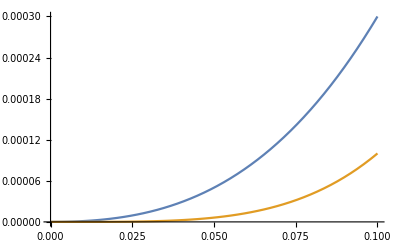

```mathematica
Plot[{P[0][x],x^4},{x,0,0.1},PlotRange->All]
```

-0.81+3.42 x-5.41 x^2+3.8 x^3

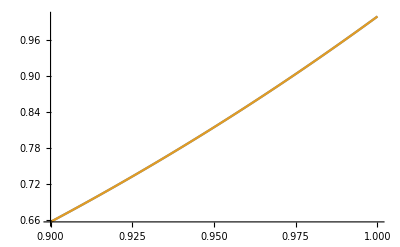

```mathematica
P[9][x_]=3.8x^3+-5.41x^2+3.42x+-0.81
Plot[{P[9][x],x^4},{x,0.9,1},PlotRange->All]
```